Generated data for Figure 3: first three dispersion curves for n=0, 1 and 2 PSSWs.

DMI on TOP only!
Single material (NiFe).

## The Eigenfrequencies -- D = 4.2 mJ/m^2

#### Some parameters needed for the code

```mathematica
B=0.03;
Δ=1;
Φ[0]=Table[0,{4}];
```

```mathematica
LL=16;
```

```mathematica
a=0.248 10^-9;  (*0.25 nm atomic spacing*)
Ms=835563; (*A/m*)
AA=1.355 10^-11;  (*J/m*)
DD =4.2 10^-3 1/1; (* i.e. This is 4.2 mJ/m^2 for 1 layer and decreases for thicker films!*)
JJ=(2 AA)/(a^2 Ms)
```

527.335

```mathematica
K[i_]:=K[i]=Which[i<LL/2+0.5,0,i>LL/2+0.5,0]
J[i_]:=J[i]=Which[i<LL/2+0.5,JJ,i>LL/2+0.5,JJ]
H[i_]:=H[i]=Which[i<LL/2+0.5,B,i>LL/2+0.5,B]
HDMI[1]=2 DD/(a Ms);
HDMI[LL]=0
```

0

```mathematica
ϕ[i_]:=ϕ[i]=0
```

#### Coding required to create dynamical matrix

For a typical plane of spins in the wall the code is:

```mathematica
acomponent[i_,y_,z_]:=acomponent[i,y,z]=H[i] Cos[ϕ[i]]+(4 π 10^-7) Ms+2 K[i] (Cos[ϕ[i]]^2-Sin[ϕ[i]]^2)+J[i] (Cos[ϕ[i]-ϕ[i-1]]+Cos[ϕ[i]-ϕ[i+1]])+4 J[i]-2 J[i] Cos[y]-2 J[i] Cos[z]
aplus[i_]:=aplus[i]=-J[i] Cos[ϕ[i]-ϕ[i+1]]
aminus[i_]:=aminus[i]=-J[i] Cos[ϕ[i]-ϕ[i-1]]
bcomponent[i_,y_,z_]:=bcomponent[i,y,z]=-H[i] Cos[ϕ[i]]-2 K[i] Cos[ϕ[i]]^2-J[i] (Cos[ϕ[i]-ϕ[i-1]]+Cos[ϕ[i]-ϕ[i+1]])-4 J[i]+2 J[i] Cos[y]+2 J[i] Cos[z]
```

```mathematica
rowa[NN_,k_,y_,z_]:=Join[Table[0,{2 k-3}],{aminus[k],0,acomponent[k,y,z],0,aplus[k]},Table[0,{2 NN-2-2 k}]]
rowb[NN_,k_,y_,z_]:=Join[Table[0,{2 k-4}],{J[k],0,bcomponent[k,y,z],0,J[k]},Table[0,{2 NN-1-2 k}]]
```

The 1st, (N/2)th, (N/2 +1)th and Nth planes all need individual codes sinse they have different exchange coupling to the planes on either side.
The codes are as follows:

```mathematica
arow1[NN_,y_,z_]:=arow1[NN,y,z]=Join[
{-HDMI[1] Sin[y] ⅈ,
H[1] Cos[ϕ[1]]+(4 π 10^-7) Ms+2 K[1] (Cos[ϕ[1]]^2-Sin[ϕ[1]]^2)+J[1] (0+Cos[ϕ[1]-ϕ[2]])+4 J[1]-2 J[1] Cos[y]-2 J[1] Cos[z],
0,
aplus[1]},
Table[0,{2 NN-4}]];
```

```mathematica
brow1[NN_,y_,z_]:=brow1[NN,y,z]=Join[
{-H[1] Cos[ϕ[1]]-2 K[1] Cos[ϕ[1]]^2-J[1] (0+Cos[ϕ[1]-ϕ[2]])-4 J[1]+2 J[1] Cos[y]+2 J[1] Cos[z],
-HDMI[1] Sin[y] ⅈ,
J[2]},
Table[0,{2 NN-3}]];
```

Note that I have kept the ANGULAR dependence in this code, which was set up for dealing with an exchange spring. It is not needed here, but it is an interesting question to see how the DMI can change the modes on an exchange spring...

```mathematica
arow50[NN_,y_,z_,β_]:=arow50[NN,y,z,β]=Join[
Table[0,{NN -3}],
{aminus[NN/2],
0,
H[NN/2] Cos[ϕ[NN/2]]+(4 π 10^-7) Ms+2 K[NN/2] (Cos[ϕ[NN/2]]^2-Sin[ϕ[NN/2]]^2)+J[NN/2] Cos[ϕ[NN/2]-ϕ[NN/2]]+(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]+4 J[NN/2]-2 J[NN/2] Cos[y]-2 J[NN/2] Cos[z],
0,
-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]},
Table[0,{NN-2}]]
```

```mathematica
brow50[NN_,y_,z_,β_]:=brow50[NN,y,z,β]=Join[
Table[0,{NN-4}],
{J[NN/2],
0,
-H[NN/2] Cos[ϕ[NN/2]]-2 K[NN/2] Cos[ϕ[NN/2]]^2-J[NN/2] Cos[ϕ[NN/2]-ϕ[NN/2-1]]-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]-4 J[NN/2]+2 J[NN/2] Cos[y]+2 J[NN/2] Cos[z],
0,
J[NN]+β (J[1]-J[NN])},
Table[0,{NN-1}]]
```

```mathematica
arow51[NN_,y_,z_,β_]:=arow51[NN,y,z,β]=Join[
Table[0,{NN-1}],
{-(J[NN/2]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]],
0,
H[NN/2+1] Cos[ϕ[NN/2+1]]+(4 π 10^-7) Ms+2 K[NN/2+1] (Cos[ϕ[NN/2+1]]^2-Sin[ϕ[NN/2+1]]^2)+(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]]+J[NN/2+1] Cos[ϕ[NN/2+1]-ϕ[NN/2+2]]+4 J[NN/2+1]-2 J[NN/2+1] Cos[y]-2 J[NN/2+1] Cos[z],
0,
aplus[NN/2+1]},
Table[0,{NN-4}]]
```

```mathematica
brow51[NN_,y_,z_,β_]:=brow51[NN,y,z,β]=Join[
Table[0,{NN-2}],
{J[NN]+β (J[1]-J[NN]),
0,
-H[NN/2+1] Cos[ϕ[NN/2+1]]-2 K[NN/2+1] Cos[ϕ[NN/2+1]]^2-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]]-J[NN/2+1] Cos[ϕ[NN/2+1]-ϕ[NN/2+2]]-4 J[NN/2+1]+2 J[NN/2+1] Cos[y]+2 J[NN/2+1] Cos[z],
0,
J[NN/2+1]},
Table[0,{NN-3}]]
```

```mathematica
arow100[NN_,y_,z_]:=Join[
Table[0,{2 NN-3}],
{aminus[NN],
-HDMI[NN] Sin[y] ⅈ,
H[NN] Cos[ϕ[NN]]+(4 π 10^-7) Ms+2 K[NN] (Cos[ϕ[NN]]^2-Sin[ϕ[NN]]^2)+J[NN] (Cos[ϕ[NN]-ϕ[NN-1]]+0)+4 J[NN]-2 J[NN] Cos[y]-2 J[NN] Cos[z]}];
```

```mathematica
brow100[NN_,y_,z_]:=Join[
Table[0,{2 NN-4}],
{J[NN-1],
0,
-H[NN] Cos[ϕ[NN]]-2 K[NN] Cos[ϕ[NN]]^2-J[NN] (Cos[ϕ[NN]-ϕ[NN-1]]+0)-4 J[NN]+2 J[NN] Cos[y]+2 J[NN] Cos[z],
-HDMI[NN] Sin[y] ⅈ}];
```

#### The dynamical matrix and eigenfrequencies

The dynamical matrix is:

```mathematica
big[NN_,y_,z_,β_]:=big[NN,y,z,β]=Join[
{arow1[NN,y,z],brow1[NN,y,z]},
Flatten[Table[{rowa[NN,j,y,z],rowb[NN,j,y,z]},{j,2,NN/2-1}],1],{arow50[NN,y,z,β],brow50[NN,y,z,β],arow51[NN,y,z,β],brow51[NN,y,z,β]},Flatten[Table[{rowa[NN,j,y,z],rowb[NN,j,y,z]},{j,NN/2+2,NN-1}],1],
{arow100[NN,y,z],brow100[NN,y,z]}]
```

The eigenfrequencies are given by (γ = 176 GHz rad/T):

```mathematica
freqs[NN_,y_,z_,β_]:=freqs[NN,y,z,β]=176/(2. π)Table[Reverse[Chop[ⅈ Eigenvalues[big[NN,y,z,β]]]]⟦k⟧,{k,1,2 NN,2}]
```

```mathematica
freqs2[NN_,y_,z_,β_]:=freqs2[NN,y,z,β]=176/(2. π) Table[Reverse[Chop[ⅈ Eigenvalues[big[NN,y,z,β]]]]⟦k⟧,{k,1,2 NN,1}]
```

#### Dispersion plots

n = 0 (quasi-uniform)

```mathematica
Table[{ky/10^6,If[freqs2[LL,ky a,0,0.5][[1]]>0,freqs2[LL,ky a,0,0.5][[1]],freqs2[LL,ky a,0,0.5][[2]]] },{ky,-100 10^6,100 10^6,1 10^6}]
```

{{-100,17.979},{-99,17.7711},{-98,17.5646},{-97,17.3593},{-96,17.1554},{-95,16.9528},{-94,16.7516},{-93,16.5516},{-92,16.3529},{-91,16.1556},{-90,15.9596},{-89,15.7648},{-88,15.5714},{-87,15.3792},{-86,15.1884},{-85,14.9988},{-84,14.8105},{-83,14.6235},{-82,14.4377},{-81,14.2533},{-80,14.0701},{-79,13.8882},{-78,13.7076},{-77,13.5282},{-76,13.3501},{-75,13.1733},{-74,12.9977},{-73,12.8234},{-72,12.6504},{-71,12.4787},{-70,12.3082},{-69,12.139},{-68,11.9711},{-67,11.8044},{-66,11.6391},{-65,11.475},{-64,11.3122},{-63,11.1507},{-62,10.9905},{-61,10.8316},{-60,10.674},{-59,10.5178},{-58,10.3628},{-57,10.2092},{-56,10.057},{-55,9.90614},{-54,9.75664},{-53,9.60854},{-52,9.46184},{-51,9.31657},{-50,9.17274},{-49,9.03038},{-48,8.88949},{-47,8.75012},{-46,8.61228},{-45,8.47601},{-44,8.34132},{-43,8.20826},{-42,8.07686},{-41,7.94716},{-40,7.81919},{-39,7.693},{-38,7.56863},{-37,7.44614},{-36,7.32558},{-35,7.20699},{-34,7.09045},{-33,6.97601},{-32,6.86375},{-31,6.75373},{-30,6.64604},{-29,6.54074},{-28,6.43794},{-27,6.33771},{-26,6.24016},{-25,6.14539},{-24,6.0535},{-23,5.96459},{-22,5.8788},{-21,5.79624},{-20,5.71702},{-19,5.64129},{-18,5.56917},{-17,5.50081},{-16,5.43633},{-15,5.37589},{-14,5.31962},{-13,5.26766},{-12,5.22016},{-11,5.17726},{-10,5.13908},{-9,5.10577},{-8,5.07745},{-7,5.05423},{-6,5.03621},{-5,5.02351},{-4,5.01619},{-3,5.01434},{-2,5.018},{-1,5.02722},{0,5.04203},{1,5.06242},{2,5.0884},{3,5.11994},{4,5.15699},{5,5.19951},{6,5.24741},{7,5.30063},{8,5.35905},{9,5.42257},{10,5.49108},{11,5.56446},{12,5.64256},{13,5.72526},{14,5.81242},{15,5.90389},{16,5.99953},{17,6.09921},{18,6.20277},{19,6.31009},{20,6.42102},{21,6.53543},{22,6.6532},{23,6.77419},{24,6.89829},{25,7.02539},{26,7.15536},{27,7.28811},{28,7.42354},{29,7.56154},{30,7.70203},{31,7.84493},{32,7.99015},{33,8.13761},{34,8.28725},{35,8.43899},{36,8.59277},{37,8.74854},{38,8.90623},{39,9.06579},{40,9.22718},{41,9.39035},{42,9.55525},{43,9.72185},{44,9.89011},{45,10.06},{46,10.2315},{47,10.4045},{48,10.5791},{49,10.7552},{50,10.9327},{51,11.1118},{52,11.2922},{53,11.4741},{54,11.6574},{55,11.8421},{56,12.0282},{57,12.2156},{58,12.4044},{59,12.5945},{60,12.786},{61,12.9788},{62,13.1729},{63,13.3683},{64,13.565},{65,13.7629},{66,13.9622},{67,14.1628},{68,14.3646},{69,14.5678},{70,14.7722},{71,14.9778},{72,15.1848},{73,15.393},{74,15.6025},{75,15.8132},{76,16.0252},{77,16.2385},{78,16.4531},{79,16.6689},{80,16.886},{81,17.1044},{82,17.3241},{83,17.545},{84,17.7672},{85,17.9907},{86,18.2155},{87,18.4415},{88,18.6689},{89,18.8975},{90,19.1275},{91,19.3587},{92,19.5912},{93,19.8251},{94,20.0602},{95,20.2967},{96,20.5345},{97,20.7736},{98,21.014},{99,21.2558},{100,21.4989}}

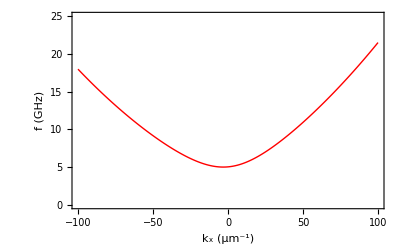

```mathematica
ListPlot[Table[{ky/10^6,If[freqs2[LL,ky a,0,0.5][[1]]>0,freqs2[LL,ky a,0,0.5][[1]],freqs2[LL,ky a,0,0.5][[2]]] },{ky,-100 10^6,100 10^6,1 10^6}],Frame->True,FrameLabel->{"k_x (μm^-1)","f (GHz)"},PlotRange->{0,25},LabelStyle->Directive[Large,Black, Bold,FontFamily->Times],Joined->True,PlotStyle->Directive[Red,Thick],FrameStyle->Directive[Black,Thick]]
```

n=1 (first PSSW)

```mathematica
Table[{ky/10^6,If[freqs2[LL,ky a,0,0.5][[3]]>0,freqs2[LL,ky a,0,0.5][[3]],freqs2[LL,ky a,0,0.5][[4]]] },{ky,-100 10^6,100 10^6,1 10^6}]
```

{{-100,588.614},{-99,588.468},{-98,588.324},{-97,588.182},{-96,588.041},{-95,587.903},{-94,587.766},{-93,587.631},{-92,587.497},{-91,587.366},{-90,587.236},{-89,587.109},{-88,586.983},{-87,586.859},{-86,586.736},{-85,586.616},{-84,586.497},{-83,586.38},{-82,586.265},{-81,586.152},{-80,586.041},{-79,585.931},{-78,585.823},{-77,585.717},{-76,585.613},{-75,585.511},{-74,585.41},{-73,585.311},{-72,585.215},{-71,585.12},{-70,585.026},{-69,584.935},{-68,584.845},{-67,584.757},{-66,584.671},{-65,584.587},{-64,584.505},{-63,584.424},{-62,584.346},{-61,584.269},{-60,584.194},{-59,584.121},{-58,584.049},{-57,583.979},{-56,583.912},{-55,583.846},{-54,583.782},{-53,583.719},{-52,583.659},{-51,583.6},{-50,583.543},{-49,583.488},{-48,583.435},{-47,583.383},{-46,583.334},{-45,583.286},{-44,583.24},{-43,583.196},{-42,583.153},{-41,583.113},{-40,583.074},{-39,583.037},{-38,583.002},{-37,582.969},{-36,582.937},{-35,582.907},{-34,582.88},{-33,582.854},{-32,582.829},{-31,582.807},{-30,582.787},{-29,582.768},{-28,582.751},{-27,582.736},{-26,582.722},{-25,582.711},{-24,582.701},{-23,582.693},{-22,582.687},{-21,582.683},{-20,582.681},{-19,582.68},{-18,582.682},{-17,582.685},{-16,582.689},{-15,582.696},{-14,582.705},{-13,582.715},{-12,582.727},{-11,582.741},{-10,582.757},{-9,582.774},{-8,582.794},{-7,582.815},{-6,582.838},{-5,582.863},{-4,582.89},{-3,582.918},{-2,582.949},{-1,582.981},{0,583.015},{1,583.05},{2,583.088},{3,583.127},{4,583.169},{5,583.212},{6,583.257},{7,583.303},{8,583.352},{9,583.402},{10,583.454},{11,583.508},{12,583.564},{13,583.621},{14,583.681},{15,583.742},{16,583.805},{17,583.87},{18,583.937},{19,584.005},{20,584.075},{21,584.147},{22,584.221},{23,584.297},{24,584.375},{25,584.454},{26,584.535},{27,584.618},{28,584.703},{29,584.79},{30,584.878},{31,584.968},{32,585.061},{33,585.154},{34,585.25},{35,585.348},{36,585.447},{37,585.548},{38,585.651},{39,585.756},{40,585.863},{41,585.971},{42,586.081},{43,586.194},{44,586.307},{45,586.423},{46,586.541},{47,586.66},{48,586.781},{49,586.904},{50,587.029},{51,587.156},{52,587.284},{53,587.414},{54,587.546},{55,587.68},{56,587.816},{57,587.954},{58,588.093},{59,588.234},{60,588.377},{61,588.522},{62,588.668},{63,588.817},{64,588.967},{65,589.119},{66,589.273},{67,589.429},{68,589.586},{69,589.746},{70,589.907},{71,590.07},{72,590.234},{73,590.401},{74,590.569},{75,590.74},{76,590.912},{77,591.086},{78,591.261},{79,591.439},{80,591.618},{81,591.799},{82,591.982},{83,592.167},{84,592.353},{85,592.542},{86,592.732},{87,592.924},{88,593.118},{89,593.313},{90,593.511},{91,593.71},{92,593.911},{93,594.114},{94,594.319},{95,594.526},{96,594.734},{97,594.944},{98,595.156},{99,595.37},{100,595.586}}

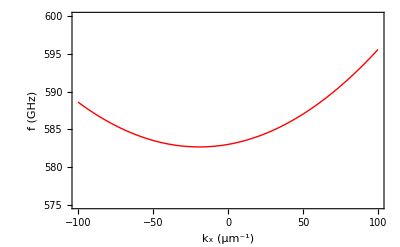

```mathematica
ListPlot[Table[{ky/10^6,If[freqs2[LL,ky a,0,0.5][[3]]>0,freqs2[LL,ky a,0,0.5][[3]],freqs2[LL,ky a,0,0.5][[4]]] },{ky,-100 10^6,100 10^6,1 10^6}],Frame->True,FrameLabel->{"k_x (μm^-1)","f (GHz)"},PlotRange->{575,600},LabelStyle->Directive[Large,Black, Bold,FontFamily->Times],Joined->True,PlotStyle->Directive[Red,Thick],FrameStyle->Directive[Black,Thick]]
```

n=2 (second PSSW)

```mathematica
Table[{ky/10^6,If[freqs2[LL,ky a,0,0.5][[5]]>0,freqs2[LL,ky a,0,0.5][[5]],freqs2[LL,ky a,0,0.5][[6]]] },{ky,-100 10^6,100 10^6,1 10^6}]
```

{{-100,2270.},{-99,2269.85},{-98,2269.71},{-97,2269.56},{-96,2269.42},{-95,2269.28},{-94,2269.15},{-93,2269.01},{-92,2268.88},{-91,2268.74},{-90,2268.61},{-89,2268.48},{-88,2268.36},{-87,2268.23},{-86,2268.11},{-85,2267.99},{-84,2267.87},{-83,2267.75},{-82,2267.63},{-81,2267.52},{-80,2267.41},{-79,2267.3},{-78,2267.19},{-77,2267.08},{-76,2266.97},{-75,2266.87},{-74,2266.77},{-73,2266.67},{-72,2266.57},{-71,2266.48},{-70,2266.38},{-69,2266.29},{-68,2266.2},{-67,2266.11},{-66,2266.02},{-65,2265.94},{-64,2265.85},{-63,2265.77},{-62,2265.69},{-61,2265.62},{-60,2265.54},{-59,2265.46},{-58,2265.39},{-57,2265.32},{-56,2265.25},{-55,2265.19},{-54,2265.12},{-53,2265.06},{-52,2265.},{-51,2264.94},{-50,2264.88},{-49,2264.82},{-48,2264.77},{-47,2264.72},{-46,2264.66},{-45,2264.62},{-44,2264.57},{-43,2264.52},{-42,2264.48},{-41,2264.44},{-40,2264.4},{-39,2264.36},{-38,2264.32},{-37,2264.29},{-36,2264.26},{-35,2264.23},{-34,2264.2},{-33,2264.17},{-32,2264.15},{-31,2264.12},{-30,2264.1},{-29,2264.08},{-28,2264.06},{-27,2264.05},{-26,2264.03},{-25,2264.02},{-24,2264.01},{-23,2264.},{-22,2263.99},{-21,2263.99},{-20,2263.99},{-19,2263.98},{-18,2263.98},{-17,2263.99},{-16,2263.99},{-15,2264.},{-14,2264.},{-13,2264.01},{-12,2264.02},{-11,2264.04},{-10,2264.05},{-9,2264.07},{-8,2264.09},{-7,2264.11},{-6,2264.13},{-5,2264.15},{-4,2264.18},{-3,2264.21},{-2,2264.24},{-1,2264.27},{0,2264.3},{1,2264.33},{2,2264.37},{3,2264.41},{4,2264.45},{5,2264.49},{6,2264.54},{7,2264.58},{8,2264.63},{9,2264.68},{10,2264.73},{11,2264.78},{12,2264.84},{13,2264.89},{14,2264.95},{15,2265.01},{16,2265.07},{17,2265.14},{18,2265.2},{19,2265.27},{20,2265.34},{21,2265.41},{22,2265.48},{23,2265.56},{24,2265.64},{25,2265.71},{26,2265.79},{27,2265.88},{28,2265.96},{29,2266.05},{30,2266.13},{31,2266.22},{32,2266.31},{33,2266.41},{34,2266.5},{35,2266.6},{36,2266.7},{37,2266.8},{38,2266.9},{39,2267.},{40,2267.11},{41,2267.21},{42,2267.32},{43,2267.44},{44,2267.55},{45,2267.66},{46,2267.78},{47,2267.9},{48,2268.02},{49,2268.14},{50,2268.26},{51,2268.39},{52,2268.52},{53,2268.65},{54,2268.78},{55,2268.91},{56,2269.04},{57,2269.18},{58,2269.32},{59,2269.46},{60,2269.6},{61,2269.75},{62,2269.89},{63,2270.04},{64,2270.19},{65,2270.34},{66,2270.49},{67,2270.65},{68,2270.8},{69,2270.96},{70,2271.12},{71,2271.28},{72,2271.45},{73,2271.61},{74,2271.78},{75,2271.95},{76,2272.12},{77,2272.29},{78,2272.47},{79,2272.64},{80,2272.82},{81,2273.},{82,2273.19},{83,2273.37},{84,2273.55},{85,2273.74},{86,2273.93},{87,2274.12},{88,2274.32},{89,2274.51},{90,2274.71},{91,2274.9},{92,2275.1},{93,2275.31},{94,2275.51},{95,2275.72},{96,2275.92},{97,2276.13},{98,2276.34},{99,2276.56},{100,2276.77}}

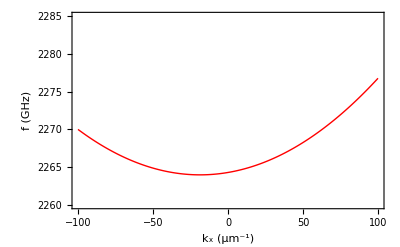

```mathematica
ListPlot[Table[{ky/10^6,If[freqs2[LL,ky a,0,0.5][[5]]>0,freqs2[LL,ky a,0,0.5][[5]],freqs2[LL,ky a,0,0.5][[6]]] },{ky,-100 10^6,100 10^6,1 10^6}],Frame->True,FrameLabel->{"k_x (μm^-1)","f (GHz)"},PlotRange->{2260,2285},LabelStyle->Directive[Large,Black, Bold,FontFamily->Times],Joined->True,PlotStyle->Directive[Red,Thick],FrameStyle->Directive[Black,Thick]]
```